```mathematica
Quit[]
```

## ME 454 Final Project. Elton Cheng Three-Link Acrobot

Gamma:

DJVal:

updateJ:

armijoCond:

Error:

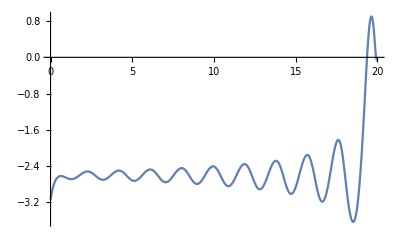

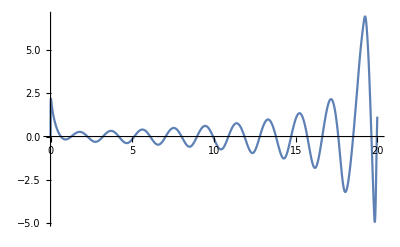

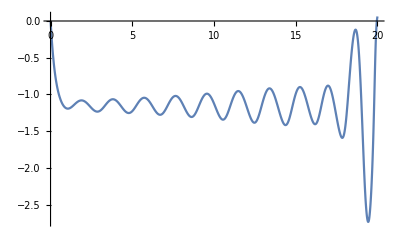

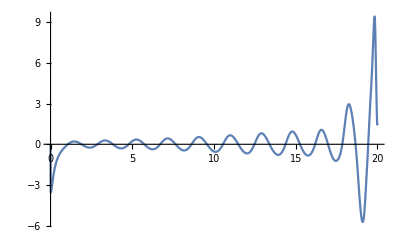

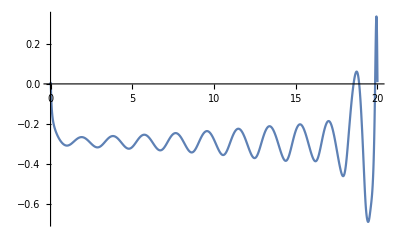

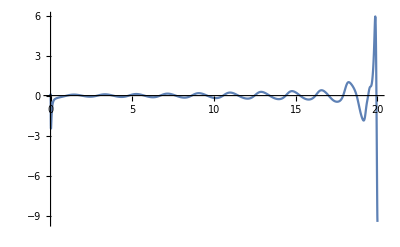

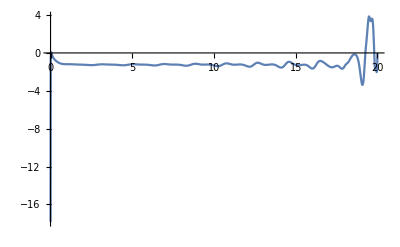

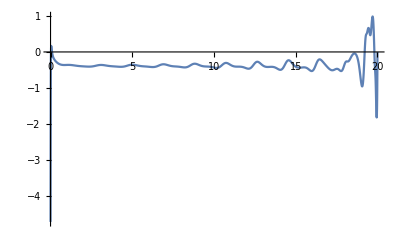

```mathematica
m1 = .2; m2 = .2; m3 = .2;g = 9.8;
l1 = .5; l2 = .5; l3 = .5;
w1 = .1; w2=.1; w3=.1;

(*Defining functions to be used*)
gMat[θ_,p_]:={{Cos[θ], -Sin[θ], 0, p[[1,1]]}, {Sin[θ], Cos[θ], 0, p[[1,2]]}, {0, 0,1, p[[1,3]]}, {0,0,0,1}}

unHat[w_]:={{w[[3,2]],w[[1,3]],w[[2,1]]}}

MomInert[h_,w_, m_]:= (m/12)*(h^2 + w^2)

InertMat[m_,J_] := {  {m, 0, 0, 0, 0, 0},
				{0, m, 0, 0, 0, 0},
				{0, 0, m, 0, 0, 0},
				{0, 0, 0, J, 0, 0},
				{0, 0, 0, 0, J, 0},
				{0, 0, 0, 0, 0, J}};

onlyRot = {{0,0,0}};

(*Translation from World frame to COM of Link 1*)
pWLink1 = {{0, l1/2,0}};
(*4x4 Rotation/Translation Transformation Matrix from World to COM of Link 1*)
gWLink1= gMat[θ1[t],onlyRot].gMat[0,pWLink1];

(*Translation from COM of Link 1 to Tip of Link 1/Base of Link 2*)
pLink1Base2 = {{0, l1/2,0}};
(*Matrix from World to Base of Link 2*)
gWBase2 = gWLink1.gMat[0,pLink1Base2];

(*Add Rotation to Base 2 frame*)
gWRotatedBase2 = gWBase2.gMat[θ2[t],onlyRot];

(*Translation from Base of Link 2 to COM of Link 2*)
pBase2Link2 = {{0, l2/2,0}};
(*Translation Transformation Matrix from Base of Link 2 to COM of Link 2*)
gWLink2 = gWRotatedBase2.gMat[0,pBase2Link2];

(*Translation from COM of Link 2 to Tip of Link 1/Base of Link 3*)
pLink2Base3 = {{0, l2/2,0}};
(*Matrix from World to Base of Link 2*)
gWBase3 = gWLink2.gMat[0,pLink2Base3];

(*Add Rotation to Base 3 frame*)
gWRotatedBase3 = gWBase3.gMat[θ3[t],onlyRot];

(*Translation from Base of Link 3 to COM of Link 3*)
pBase3Link3 = {{0, l3/2,0}};
(*Translation Transformation Matrix from Base of Link 3 to COM of Link 3*)
gWLink3 = gWRotatedBase3.gMat[0,pBase3Link3];

(*Translation from COM of Link 3 to Tip of Link 3*)
pLink3EE = {{0, l3/2,0}};
(*Matrix from World to Base of Link 2*)
gWEE = gWLink3.gMat[0,pLink3EE];

(*Link 1*)
gL1p1 = gMat[0,{{-w1/2,l1/2,0}}];
gwL1p1 = gWLink1.gL1p1;

gL1p2 = gMat[0,{{w1/2,l1/2,0}}];
gwL1p2 = gWLink1.gL1p2;

gL1p3 = gMat[0,{{w1/2,-l1/2,0}}];
gwL1p3 = gWLink1.gL1p3;

gL1p4 = gMat[0,{{-w1/2,-l1/2,0}}];
gwL1p4 = gWLink1.gL1p4;

(*Link 2*)
gL2p1 = gMat[0,{{-w2/2,l2/2,0}}];
gwL2p1 = gWLink2.gL2p1;

gL2p2 = gMat[0,{{w2/2,l2/2,0}}];
gwL2p2 = gWLink2.gL2p2;

gL2p3 = gMat[0,{{w2/2,-l2/2,0}}];
gwL2p3 = gWLink2.gL2p3;

gL2p4 = gMat[0,{{-w2/2,-l2/2,0}}];
gwL2p4 = gWLink2.gL2p4;

(*Link 3*)
gL3p1 = gMat[0,{{-w3/2,l3/2,0}}];
gwL3p1 = gWLink3.gL3p1;

gL3p2 = gMat[0,{{w3/2,l3/2,0}}];
gwL3p2 = gWLink3.gL3p2;

gL3p3 = gMat[0,{{w3/2,-l3/2,0}}];
gwL3p3 = gWLink3.gL3p3;

gL3p4 = gMat[0,{{-w3/2,-l3/2,0}}];
gwL3p4 = gWLink3.gL3p4;

(*Defining the Twists for each link*)
V1hat = Inverse[gWLink1].D[gWLink1,t];
V2hat = Inverse[gWLink2].D[gWLink2,t];
V3hat = Inverse[gWLink3].D[gWLink3,t];

wHLink1 = V1hat[[1;;3,1;;3]];
wHLink2 = V2hat[[1;;3,1;;3]];
wHLink3 = V3hat[[1;;3,1;;3]];

wLink1=unHat[wHLink1][[1]];
wLink2=unHat[wHLink2][[1]];
wLink3=unHat[wHLink3][[1]];

RTdpLink1 = V1hat[[1;;3,4]];
RTdpLink2 = V2hat[[1;;3,4]];
RTdpLink3 = V3hat[[1;;3,4]];

VLink1 = {{RTdpLink1[[1]]},{RTdpLink1[[2]]},{RTdpLink1[[3]]},{wLink1[[1]]},{wLink1[[2]]},{wLink1[[3]]} }; 
VLink2 = {{RTdpLink2[[1]]},{RTdpLink2[[2]]},{RTdpLink2[[3]]},{wLink2[[1]]},{wLink2[[2]]},{wLink2[[3]]} };
VLink3 = {{RTdpLink3[[1]]},{RTdpLink3[[2]]},{RTdpLink3[[3]]},{wLink3[[1]]},{wLink3[[2]]},{wLink3[[3]]} };

(*Calculating KE for each Link*)
InertMatLink1 = InertMat[m1,MomInert[l1, w1,m1]];
InertMatLink2 = InertMat[m2,MomInert[l2, w2,m2]];
InertMatLink3 = InertMat[m3,MomInert[l3, w3,m3]];

KE1= (1/2*Transpose[VLink1].InertMatLink1.VLink1)[[1,1]];
KE2= (1/2*Transpose[VLink2].InertMatLink2.VLink2)[[1,1]];
KE3= (1/2*Transpose[VLink3].InertMatLink3.VLink3)[[1,1]];

L = Simplify[(KE1 + KE2 + KE3) - (g*( m1*gWLink1[[2,4]] + m2*gWLink2[[2,4]] +m3*gWLink3[[2,4]]))];

(*θ1*)
eqLθ1 = D[D[L,θ1'[t]],t]-D[L,θ1[t]];

(*θ2*)
eqLθ2 = D[D[L,θ2'[t]],t]-D[L,θ2[t]];

(*θ3*)
eqLθ3 = D[D[L,θ3'[t]],t]-D[L,θ3[t]];

eqθ1 = eqLθ1 == 0;
eqθ2 = eqLθ2 == u1;
eqθ3 = eqLθ3 == u2;

β = .7;
α=.4;

Qval = .1;
Rval = .0005;
P1val = .1;

R = DiagonalMatrix[{Rval, Rval}];
Q = DiagonalMatrix[{Qval,0,Qval,0,Qval,0}];
P1 = DiagonalMatrix[{P1val,0,P1val,0,P1val,0}];

Rr = DiagonalMatrix[{Rval, Rval}];
Qr = DiagonalMatrix[{Qval,0,Qval,0,Qval,0}];
P1r = DiagonalMatrix[{P1val + .9,0,P1val,0,P1val,0}];

initcon = {θ1[0]==-Pi,θ2[0]==0,θ3[0]==0, θ1'[0]==0,θ2'[0]==0,θ3'[0]==0};

θ1dyn = Solve[{eqθ1},{θ1''[t]},{t}][[1,1,2]];
θ2dyn = Solve[{eqθ2},{θ2''[t]},{t}][[1,1,2]];
θ3dyn = Solve[{eqθ3},{θ3''[t]},{t}][[1,1,2]];

X[t]={θ1[t],θ1'[t],θ2[t],θ2'[t],θ3[t],θ3'[t]};
X'[t]={θ1'[t],θ1dyn,θ2'[t],θ2dyn,θ3'[t],θ3dyn};
U = {u1,u2};

XD={{.32,0,0,0,0,0}};

l = (.5*{X[t]}.Q.Transpose[{X[t]}] + .5*{U}.R.Transpose[{U}])[[1,1]];

A = D[X'[t],{X[t]}];
B = D[X'[t],{U}];
a[t]=Transpose[{D[l,{X[t]}]}];
b[t]={D[l,{U}]};
DL = Join[a[t], {{b[t][[1,1]]}},{{b[t][[1,2]]}}];

Pmat[t_] := Array[P[#1,#2][t]&,{6,6}];
Pdotmat[t_] := Array[P[#1,#2]'[t]&,{6,6}];
rmat[t_] := Array[r[#1,#2][t]&,{6,1}];
rdotmat[t_] := Array[r[#1,#2]'[t]&,{6,1}];
zmat[t_] := Array[z[#1,#2][t]&,{6,1}];
zdotmat[t_] := Array[z[#1,#2]'[t]&,{6,1}];

Prmat[t_] := Array[Pr[#1,#2][t]&,{6,6}];
Prdotmat[t_] := Array[Pr[#1,#2]'[t]&,{6,6}];

J[ξsol_]:=(NIntegrate[l/.ξsol,{t,0,T}, MaxRecursion->20] + .5*(({X[t]}/.ξsol/.t->T)-XD).P1.Transpose[((({X[t]}/.ξsol/.t->T)-XD))])[[1,1]];
DJ[ξsol_,ζval_]:=NIntegrate[{Flatten[DL]/.ξsol}.ζval,{t,0,T}, MaxRecursion->20];
xsol[u1val_,u2val_]:=NDSolve[{{θ1''[t]==θ1dyn, θ2''[t]==θ2dyn,θ3''[t]==θ3dyn}/.{u1-> u1val,u2->u2val}, initcon},{θ1[t],θ1'[t],θ2[t],θ2'[t],θ3[t],θ3'[t],θ1''[t],θ2''[t],θ3''[t]},{t,0,T}][[1]];

Peq[t_]:= -Pdotmat[t]==  Pmat[t].A + Transpose[A].Pmat[t]-Pmat[t].B.Inverse[R].Transpose[B].Pmat[t] + Q;
Psol[xsol_,u1val_,u2val_]:=NDSolve[{{Peq[t]/.xsol}/.u1-> u1val/.u2-> u2val,Pmat[T]==P1},{Pmat[t]},{t,0,T}][[1,1]];

Preq[t_]:= -Prdotmat[t]==  Prmat[t].A + Transpose[A].Prmat[t]-Prmat[t].B.Inverse[Rr].Transpose[B].Prmat[t] + Qr;
Prsol[xsol_,u1val_,u2val_]:=NDSolve[{{Preq[t]}/.xsol/.u1-> u1val/.u2-> u2val,Prmat[T]==P1r},{Prmat[t]},{t,0,T}][[1,1]];

req[t_]:= -rdotmat[t] == ((Transpose[A - B.Inverse[R].Transpose[B].Pmat[t]].rmat[t] + a[t]-Pmat[t].B.Inverse[R].Transpose[b[t]]));
rsol[psol_,xsol_,u1val_,u2val_]:=NDSolve[{{req[t]}/.psol/.xsol/.u1->u1val/.u2->u2val,rmat[T]==Transpose[((({X[t]}/.xsol/.t->T)-XD)).P1]},{rmat[t]},{t,0,T}][[1,1]];

veq[t_]:= -Inverse[R].Transpose[B].Pmat[t].zmat[t]-Inverse[R].Transpose[B].rmat[t]-Inverse[R].Transpose[b[t]];
zeq[t_]:= (zdotmat[t]== A.zmat[t] + B.veq[t]);
zsol[rsol_,psol_,xsol_,u1val_,u2val_]:= NDSolve[{zeq[t]/.rsol/.psol/.xsol/.u1->u1val/.u2->u2val,zmat[0]=={{0},{0},{0},{0},{0},{0}}},{zmat[t]},{t,0,T}][[1,1]];

Keq[xsol_,prsol_]:=-Inverse[Rr].Transpose[B].Prmat[t]/.prsol/.xsol;

Proj[ksol_,ξbar_]:=Module[{},
unew = (U/.ξbar)+ksol.(X[t]-(X[t]/.ξbar));
u1new = unew[[1]];
u2new = unew[[2]];
newXSol =  xsol[u1new,u2new];
unew = unew/.newXSol;
newξVals = Join[newXSol,{u1->unew[[1]],u2->unew[[2]]}];
Return[newξVals];
];

T =20;
u1Init = 0;
u2Init = 0;
ϵ = 10^0;
error = 100;
testx = xsol[u1Init, u2Init];

ξVals = Join[testx,{u1->u1Init,u2->u2Init}];
γ= 0;
updateJ = 0;
DJVal = 0;
armijoCond = 0;

Print["Gamma: ", Dynamic[γ]];
Print["DJVal: ",Dynamic[DJVal]];
Print["updateJ: ", Dynamic[updateJ]];
Print["armijoCond: ", Dynamic[armijoCond]];
Print["Error: ", Dynamic[error]];


While[error > ϵ,
testx = ξVals[[1;;9]];
u1Init = ξVals[[10,2]];
u1Init = ξVals[[11,2]];

testPr = Prsol[testx,u1Init, u2Init];
Prvals = Flatten[Thread[Flatten[testPr[[1]]]-> Flatten[testPr[[2]]]]];

ksol = Keq[testx,Prvals];

testP = Psol[testx,u1Init, u2Init];
Pvals = Flatten[Thread[Flatten[testP[[1]]]-> Flatten[testP[[2]]]]];

testr = rsol[Pvals,testx,u1Init, u2Init];
rVals = Flatten[Thread[Flatten[testr[[1]]]-> Flatten[testr[[2]]]]];

testz = zsol[testx, Pvals, rVals, u1Init, u2Init];
zVals = Flatten[Thread[Flatten[testz[[1]]]-> Flatten[testz[[2]]]]];


testv = veq[t]/.zVals/.Pvals/.rVals/.testx/.u1->u1Init/.u2->u2Init;
V1=ListInterpolation[Table[testv[[1]]/.t->tval,{tval,0,T,.01}],{{0,T}}];
V2=ListInterpolation[Table[testv[[2]]/.t->tval,{tval,0,T,.01}],{{0,T}}];

ζVals = Join[testz[[2]],{{V1[t]}, {V2[t]}}];

n = 0;
γ= β^n;

updateξ = Flatten[Thread[ξVals[[{1,2,3,4,5,6,10,11},1]]-> Flatten[ξVals[[{1,2,3,4,5,6,10,11},2]] + γ*ζVals]]];

ξValsPlus = Proj[ksol,updateξ];

updateJ = J[ξValsPlus];

ξi = Proj[ksol,ξVals];

DJVal = DJ[ξi,ζVals][[1,1]];

JVal = J[ξi];

armijoCond = (JVal + α*γ*DJVal);

While[ updateJ > armijoCond,
n = n+1;
γ= β^n;
updateξ = Flatten[Thread[ξVals[[{1,2,3,4,5,6,10,11},1]]-> Flatten[ξVals[[{1,2,3,4,5,6,10,11},2]] + γ*ζVals]]];
ξValsPlus = Proj[ksol,updateξ];
updateJ = J[ξValsPlus];
armijoCond = (JVal + α*γ*DJVal);
];
error = Norm[DJ[ξValsPlus,ζVals]];
ξVals = ξValsPlus;
ξVals[[10,2]] = ListInterpolation[Table[ξVals[[10,2]]/.t->tval,{tval,0,T,.01}],{{0,T}}][t];
ξVals[[11,2]] = ListInterpolation[Table[ξVals[[11,2]]/.t->tval,{tval,0,T,.01}],{{0,T}}][t];
];

Plot[ξVals[[1,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[2,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[3,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[4,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[5,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[6,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[10,2]],{t,0,T}, PlotRange->All]
Plot[ξVals[[11,2]],{t,0,T}, PlotRange->All]

BoxPoint[g_,t1_,ξVals_]:={g[[1,4]]/.ξVals/.t->t1,g[[2,4]]/.ξVals/.t->t1};
Solution = Table[Show[{
Graphics[{Red,Polygon[{BoxPoint[gwL1p1,t,ξVals],BoxPoint[gwL1p2,t,ξVals],BoxPoint[gwL1p3,t,ξVals],BoxPoint[gwL1p4,t,ξVals]}]}],
Graphics[{Blue,Polygon[{BoxPoint[gwL2p1,t,ξVals],BoxPoint[gwL2p2,t,ξVals],BoxPoint[gwL2p3,t,ξVals],BoxPoint[gwL2p4,t,ξVals]}]}],
Graphics[{Green,Polygon[{BoxPoint[gwL3p1,t,ξVals],BoxPoint[gwL3p2,t,ξVals],BoxPoint[gwL3p3,t,ξVals],BoxPoint[gwL3p4,t,ξVals]}]}]},
PlotRange->{{-2,2},{-2,2}}],{t,0,T,.1}];
ListAnimate[Solution]
(*Export["solution.avi",Solution]*)
```